```mathematica
lst=Table[0,8,61];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
```

General::munfl: 8.59599×10^-302 1.484×10^-16 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.32866×10^-292 (-4.75397×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.59599×10^-302 (-4.75397×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Export["F:\\ThesisProject\\RESULTS\\16082023_corr_modified\\corr_ana_newform.dat",lst,"Table"];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},Joined->True]]
```

-Graphics-

{{-2.63509×10^-14,-3.23395×10^-14,-3.95375×10^-14,-4.81861×10^-14,-5.85746×10^-14,-7.10498×10^-14,-8.60277×10^-14,-1.04007×10^-13,-1.25586×10^-13,-1.51482×10^-13,-1.82556×10^-13,-2.19838×10^-13,-2.64566×10^-13,-3.18223×10^-13,-3.82589×10^-13,-4.59797×10^-13,-5.52404×10^-13,-6.6348×10^-13,-7.96702×10^-13,-9.56483×10^-13,-1.14811×10^-12,-1.37794×10^-12,-1.65357×10^-12,-1.98412×10^-12,-2.38055×10^-12,-2.85596×10^-12,-3.42612×10^-12,-4.10989×10^-12,-4.92992×10^-12,-5.9134×10^-12,-7.09297×10^-12,7.137×10^-12,5.95136×10^-12,4.96262×10^-12,4.1381×10^-12,3.45053×10^-12,2.87716×10^-12,2.39902×10^-12,2.00031×10^-12,1.66782×10^-12,1.39056×10^-12,1.15936×10^-12,9.66557×10^-13,8.05783×10^-13,6.71715×10^-13,5.59917×10^-13,4.6669×10^-13,3.8895×10^-13,3.24124×10^-13,2.70067×10^-13,2.2499×10^-13,1.87402×10^-13,1.56058×10^-13,1.29922×10^-13,1.08128×10^-13,8.99556×10^-14,7.48026×10^-14,6.21677×10^-14,5.16326×10^-14,4.28485×10^-14,3.55245×10^-14},{0.0000735264,0.0000881719,0.000105735,0.000126795,0.000152051,0.000182338,0.000218657,0.000262211,0.00031444,0.000377072,0.00045218,0.000542248,0.000650256,0.000779778,0.0009351,0.00112136,0.00134472,0.00161257,0.00193377,0.00231895,0.00278085,0.00333476,0.003999,0.00479555,0.00575076,0.00689623,0.00826987,0.00991712,0.0118925,0.0142613,0.017147,0.0193949,0.0204762,0.0209446,0.0210794,0.0210281,0.0208703,0.0206492,0.0203893,0.0201046,0.019804,0.0194928,0.019175,0.0188532,0.0185293,0.018205,0.0178814,0.0175594,0.0172399,0.0169233,0.0166102,0.0163009,0.0159958,0.015695,0.0153987,0.0151071,0.0148202,0.0145381,0.0142609,0.0139884,0.0137209},{0.000141771,0.00017001,0.000203874,0.000244482,0.00029318,0.000351578,0.000421607,0.000505585,0.000606291,0.000727056,0.000871876,0.00104554,0.0012538,0.00150354,0.00180302,0.00216216,0.00259284,0.0031093,0.00372862,0.00447132,0.00536194,0.00642997,0.00771073,0.00924661,0.0110884,0.0132971,0.0159457,0.0191218,0.0229306,0.0274981,0.0330494,0.0370624,0.0386491,0.03912,0.0390523,0.0387107,0.0382203,0.0376428,0.0370109,0.0363436,0.0356529,0.0349472,0.0342326,0.0335139,0.0327948,0.0320784,0.031367,0.0306625,0.0299665,0.0292802,0.0286045,0.0279401,0.0272877,0.0266475,0.02602,0.0254051,0.0248031,0.0242139,0.0236375,0.0230739,0.0225229},{0.000200704,0.000240681,0.000288621,0.000346111,0.000415052,0.000497724,0.000596864,0.000715752,0.00085832,0.00102929,0.00123431,0.00148016,0.00177499,0.00212854,0.00255252,0.00306095,0.00367065,0.00440179,0.00527857,0.00632999,0.00759084,0.00910283,0.010916,0.0130903,0.0156977,0.0188245,0.0225741,0.0270706,0.0324626,0.0389288,0.0467634,0.0517078,0.0529753,0.0529143,0.052315,0.05146,0.0504608,0.0493697,0.0482166,0.047022,0.045801,0.0445656,0.0433255,0.0420884,0.0408604,0.0396466,0.0384509,0.0372762,0.0361249,0.0349989,0.0338993,0.0328271,0.0317828,0.0307668,0.0297791,0.0288197,0.0278883,0.0269846,0.0261082,0.0252586,0.0244352},{0.000248171,0.000297604,0.000356882,0.000427969,0.000513214,0.00061544,0.000738027,0.000885032,0.00106132,0.00127272,0.00152623,0.00183023,0.00219479,0.00263196,0.00315621,0.00378489,0.00453878,0.00544285,0.00652699,0.00782708,0.00938613,0.0112557,0.0134977,0.0161863,0.0194104,0.0232766,0.027913,0.0334729,0.0401403,0.0481357,0.0577931,0.0626923,0.0630187,0.062174,0.0608911,0.0593666,0.0576814,0.0558856,0.054017,0.0521055,0.0501751,0.0482449,0.0463302,0.044443,0.0425925,0.0407858,0.0390282,0.0373236,0.0356744,0.0340823,0.0325483,0.0310724,0.0296543,0.0282935,0.0269889,0.0257392,0.024543,0.0233989,0.022305,0.0212598,0.0202615},{0.000283948,0.000340507,0.000408331,0.000489665,0.0005872,0.000704162,0.000844421,0.00101262,0.00121432,0.00145619,0.00174625,0.00209408,0.00251119,0.00301139,0.00361121,0.00433052,0.0051931,0.00622749,0.00746793,0.00895544,0.0107392,0.0128784,0.0154435,0.0185197,0.0222086,0.0266322,0.031937,0.0382984,0.0459269,0.055075,0.0660953,0.0700902,0.0693133,0.0676291,0.0655004,0.0630732,0.0604455,0.0576937,0.0548785,0.0520476,0.0492382,0.0464787,0.0437906,0.0411896,0.038687,0.0362903,0.0340039,0.0318301,0.0297693,0.0278204,0.0259813,0.024249,0.0226199,0.0210902,0.0196555,0.0183114,0.0170534,0.015877,0.0147777,0.0137512,0.0127932},{0.000309351,0.00037097,0.000444862,0.000533472,0.000639733,0.000767159,0.000919967,0.00110321,0.00132296,0.00158647,0.00190248,0.00228142,0.00273585,0.0032808,0.00393429,0.00471794,0.0056577,0.00678463,0.00813604,0.00975663,0.0117,0.0140305,0.0168252,0.0201765,0.0241954,0.0290148,0.0347942,0.0417247,0.0500358,0.0600022,0.0719843,0.0745765,0.0727749,0.0700649,0.0667795,0.0631275,0.0592695,0.0553284,0.0513971,0.0475443,0.0438199,0.0402583,0.0368823,0.0337055,0.0307341,0.0279694,0.0254083,0.0230448,0.0208712,0.0188779,0.0170547,0.015391,0.013876,0.0124989,0.0112491,0.0101167,0.00909202,0.0081659,0.00732981,0.00657577,0.00589636},{0.000326527,0.000391566,0.000469561,0.000563091,0.000675251,0.000809752,0.000971044,0.00116446,0.00139641,0.00167455,0.0020081,0.00240809,0.00288775,0.00346295,0.00415272,0.00497989,0.00597182,0.00716132,0.00858776,0.0102983,0.0123496,0.0148095,0.0177593,0.0212968,0.0255388,0.0306258,0.036726,0.0440413,0.0528138,0.0633336,0.0759631,0.0770432,0.074102,0.0699885,0.0651801,0.0600241,0.0547709,0.0495971,0.0446229,0.039926,0.0355527,0.031526,0.0278522,0.0245259,0.0215334,0.0188562,0.0164724,0.0143587,0.0124915,0.0108473,0.0094038,0.00813982,0.00703568,0.00607326,0.00523601,0.00450899,0.00387873,0.0033332,0.00286168,0.00245467,0.00210378}}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\corr_ana.dat",lst]
corr0=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_0.dat",Number];
corr1=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_1.dat",Number];
corr2=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_2.dat",Number];
corr3=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_3.dat",Number];
corr4=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_4.dat",Number];
corr5=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_5.dat",Number];
corr6=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_6.dat",Number];
corr7=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_7.dat",Number];
```

F:\ThesisProject\RESULTS\26052023_corr_modified\corr_ana.dat

```mathematica
plst=Table[0,{i,8},{j,31},{k,2}];
For[i=0,i<8,i++,plst[[i+1]]=Transpose[{Table[i,{i,-30,30}],lst[[i+1]]}]];
```

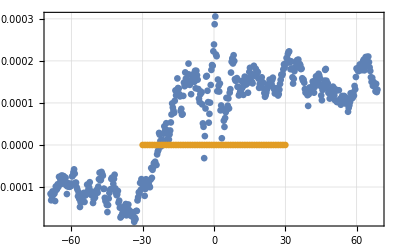

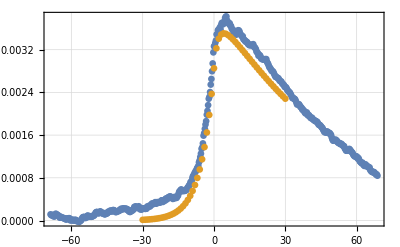

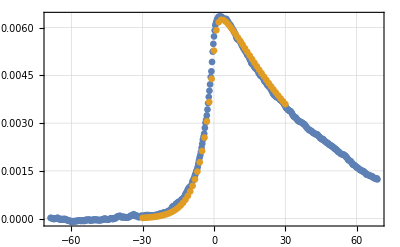

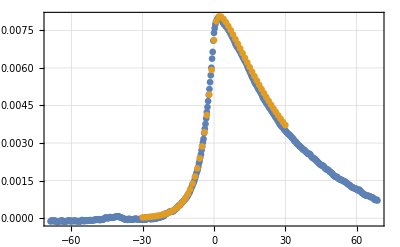

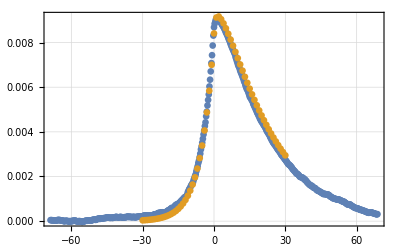

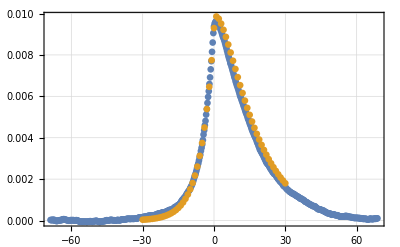

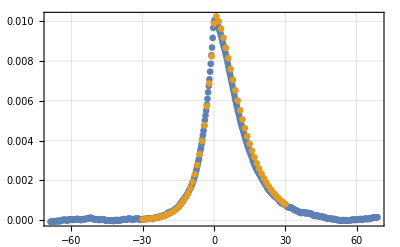

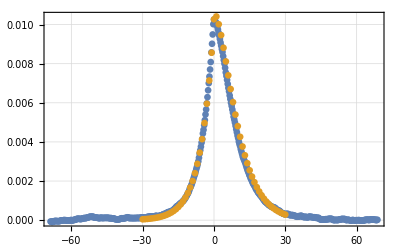

```mathematica
scalF=5.5;
pcr0=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr0}];

ListPlot[{pcr0,plst[[1]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr1=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr1}];

ListPlot[{pcr1,plst[[2]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr2=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr2}];

ListPlot[{pcr2,plst[[3]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr3=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr3}];

ListPlot[{pcr3,plst[[4]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr4=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr4}];

ListPlot[{pcr4,plst[[5]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr5=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr5}];

ListPlot[{pcr5,plst[[6]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr6=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr6}];

ListPlot[{pcr6,plst[[7]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr7=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr7}];

ListPlot[{pcr7,plst[[8]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
```

```mathematica
(**)
```

```mathematica
dlst=Table[0,8,31];
For[gg=0,gg<8,gg++,dlst[[gg+1]]=Table[lst[[gg+1,31-i]]-lst[[gg+1,31+i]],{i,-30,0}]];
```

```mathematica
Rasterize[ListPlot[dlst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,0},Joined->True]]
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\DCtau_eq.dat",dlst];
```

-Graphics-

```mathematica
(*24.05.2023*)
```

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

```mathematica
Rasterize[ListPlot[maxc,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},Joined->True]]
```

-Graphics-

```mathematica
Rasterize[ListPlot[maxt,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
(*25.05.2023*)
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat",lst]
```

F:\ThesisProject\RESULTS\25052023_extrema\h10.dat

```mathematica
ilst=Import["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat","Table"];
```

```mathematica
ilst[[1]]={0,Infinity};
```

```mathematica
fitMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,1]]}];
fitTMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,2]]}];
```

FittedModel[-0.0000219197+0.00102339 x-0.00016372 x^2+0.0000119369 x^3-3.28706×10^-7 x^4]

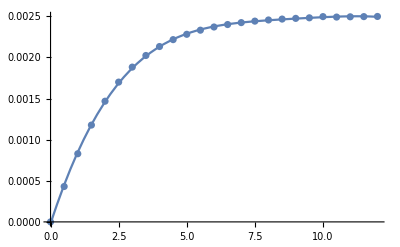

```mathematica
nlm=NonlinearModelFit[fitMax,a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
Show[ListPlot[ilst[[All,1]],DataRange->{0,12},PlotRange->All],Plot[nlm[x],{x,0,12}]]
```

FittedModel[18.7195-1.50103/x-4.71804 x+0.371601 x^2-0.00456264 x^3-0.000364738 x^4]

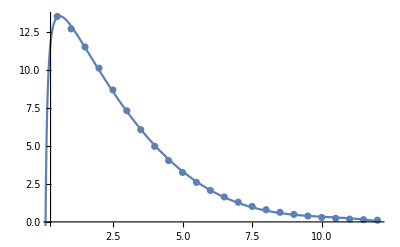

```mathematica
nlmt=NonlinearModelFit[fitTMax[[2;;25]],a+b x+c x^2+d x^3+e x^4+f x^(-1),{a,b,c,d,e,f},x]
Show[ListPlot[ilst[[All,2]],DataRange->{0,12},PlotRange->All],Plot[nlmt[x],{x,0,12}]]
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\fit.dat",{nlm//Normal,nlmt//Normal}]
```

F:\ThesisProject\RESULTS\25052023_extrema\fit.dat

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

(0 | 0.0562453 | 0.0887259 | 0.102058 | 0.107213 | 0.10916
0 | 0.0233935 | 0.0353066 | 0.0400117 | 0.0418152 | 0.0424933
0 | 0.00625079 | 0.0091827 | 0.0102691 | 0.0106702 | 0.0108184
0 | 0.0014678 | 0.00213307 | 0.0023707 | 0.00245623 | 0.00248632
0 | 0.000332398 | 0.000481201 | 0.000533496 | 0.000552089 | 0.000558832)

(0 | 0.269867 | 0.129315 | 0.052779 | 0.0202246 | 0.00755684
0 | 0.964786 | 0.476559 | 0.200015 | 0.0778965 | 0.0293205
0 | 3.3005 | 1.62697 | 0.679211 | 0.26338 | 0.0989795
0 | 10.101 | 4.96469 | 2.0674 | 0.800207 | 0.301444
0 | 28.5502 | 13.9992 | 5.81894 | 2.24996 | 0.843757)

{{38.3194,41.5955,43.0497,43.6496,43.9041},{15.9377,16.552,16.8776,17.0241,17.0908},{4.25861,4.30493,4.3317,4.34415,4.35119},{1.,1.,1.,1.,1.},{0.22646,0.225591,0.225038,0.224771,0.224763}}

FittedModel[-1.02185+44.2437/x]

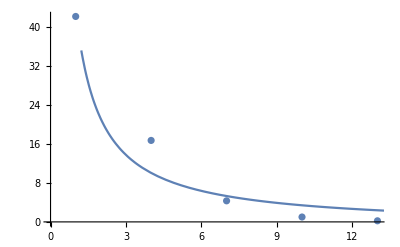

```mathematica
rate=Table[maxc[[i,2;;6]]/maxc[[4,2;;6]],{i,1,5}]
ratefit=Mean[Transpose[rate]];
ratefit=Transpose[{{1,4,7,10,13},ratefit}];
line=NonlinearModelFit[ratefit,a+b/x,{a,b,c,d},x]
Show[ListPlot[ratefit],Plot[line[x],{x,0,15}]]
```

{{0.0267168,0.0260469,0.0255292,0.0252742,0.0250688},{0.0955137,0.0959895,0.0967474,0.0973454,0.0972668},{0.326749,0.327708,0.328534,0.32914,0.328351},{1.,1.,1.,1.,1.},{2.82647,2.81974,2.81462,2.81173,2.79905}}

FittedModel[-0.0305447+0.0338354 ⅇ^(0.340939 x)]

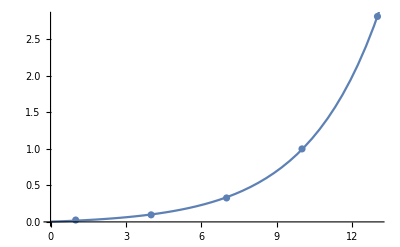

```mathematica
ratet=Table[maxt[[i,2;;6]]/maxt[[4,2;;6]],{i,1,5}]
ratetfit=Mean[Transpose[ratet]];
ratetfit=Transpose[{{1,4,7,10,13},ratetfit}];
linet=NonlinearModelFit[ratetfit,a+b Exp[c x],{a,b,c,d},x]
Show[ListPlot[ratetfit],Plot[linet[x],{x,0,15}]]
```

```mathematica
lmtM0=Limit[matJump,g->0]
eigVa0=Eigenvalues[lmtM0]
eigVeR0=Eigenvectors[lmtM0]
eigVeL0=Eigenvectors[Transpose[lmtM0]];
eigNVeL0=Table[eigVeL0[[i]]/(eigVeL0[[i]].eigVeR0[[i]]),{i,1,8}]
nessDist0=Limit[nessDist,g->0]
```

{{-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0,ⅇ^(h/4),0,0,0},{ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),0,0},{ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4),0,0,ⅇ^(-h/4),0},{0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4),0,0,0,ⅇ^(-3 h/4)},{ⅇ^(h/4),0,0,0,-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0},{0,ⅇ^(-h/4),0,0,ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4)},{0,0,ⅇ^(-h/4),0,ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4)},{0,0,0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4)}}

{0,-4 ⅇ^(-h/4),-2 ⅇ^(-h/4),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h-√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h+√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,1],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,2],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,3]}

{{ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1,ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1},6,{(ⅇ^(-3 h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[48 ⅇ^111+1+1+#1^3&,3]+12+3 ⅇ^h 1^4+Root[48 ⅇ^1+1+1+#1^3&,3]^5))/(2 (24 ⅇ^(3 h/2)+6 ⅇ^(h/2) Root[48 ⅇ^1+(1) #1+(1) 1+#1^3&,3]+3+ⅇ^1 1^2+ⅇ^h Root[48 ⅇ^1+1+1+#1^3&,3]^2)),1/(2 1),4,1,1}}
 |  |  |  |

{{1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2))},6,{(ⅇ^(-h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[1]+92 ⅇ^1 Root[1&,3]+10+1+3 ⅇ^h 1^4+Root[1&,3]^5))/(2 1 (1+(1)^2/(1)^2+1/1+1+(ⅇ^1 1)/(2 1^2)+(ⅇ^(-2 h) (1)^2)/(4 (1)^2))),6,1/1}}
 |  |  |  |

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
Limit[nessDist,g->Infinity]
```

{1/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),0,0,0,0,ⅇ^h/((1+ⅇ^(h/2))^2)}

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
xExp0=Dot[nessDist0,xL];
yExp0=Dot[nessDist0,yL];
{seigenVa,seigenVeL,nseigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigVa0,eigVeL0,eigNVeL0,eigVeR0,nessDist0,xExp0,yExp0};
```

```mathematica
lst[[3]]=Table[fCtauN[i]/.h->7,{i,-30,0}]~Join~Table[fCtauP[i]/.h->7,{i,1,30}];
```

General::munfl: 8.59599×10^-302 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.32866×10^-292 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Rasterize[ListPlot[{lst[[3]],lst[[1]],lst[[2]]},DataRange->{-30,30},PlotRange->All,Joined->True,AxesLabel->{"τ","C(τ)"},PlotLegends->Placed[{"γ→0","γ=10","γ→∞"},{0.8,0.8}]]]
```

-Graphics-

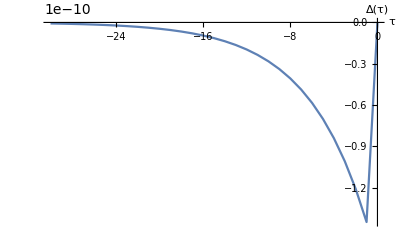

```mathematica
ListPlot[Table[lst[[31+i]]-lst[[31-i]],{i,30,0,-1}],DataRange->{-30,0},Joined->True,AxesLabel->{"τ","Δ(τ)"}]
```

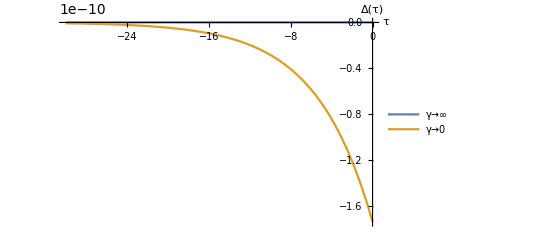

```mathematica
Plot[{fIDCtau[t]/.h->7,fDCtau[t]/.h->7},{t,-30,0},PlotRange->All,AxesLabel->{"τ","Δ(τ)"},PlotLegends->Placed[{"γ→∞","γ→0"},{0.1,0.8}]]
```

```mathematica
(*EQ degeneration*)
x1=1;
x2=1;
yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]))];
matJump=Transpose[({{-(fH[h,1]*3), fH[h,1], fH[h,1], 0, fH[h,1], 0, 0, 0}, {fH[h,2], -(fH[h,2]*3), 0, fH[h,2], 0, fH[h,2], 0, 0}, {fH[h,3], 0, -(fH[h,3]*3), fH[h,3], 0, 0, fH[h,3], 0}, {0, fH[h,4], fH[h,4], -(fH[h,4]*3), 0, 0, 0, fH[h,4]}, {fH[h,5], 0, 0, 0, -(fH[h,5]*3), fH[h,5], fH[h,5], 0}, {0, fH[h,6], 0, 0, fH[h,6], -(fH[h,6]*3), 0, fH[h,6]}, {0, 0, fH[h,7], 0, fH[h,7], 0, -(fH[h,7]*3), fH[h,7]}, {0, 0, 0, fH[h,8], 0, fH[h,8], fH[h,8], -(fH[h,8])}})];
eigenVa=Eigenvalues[matJump];
eigenVeR=Eigenvectors[matJump];
eigenVeL=Eigenvectors[Transpose[matJump]];
```

```mathematica
xL={1,2,3,4,1,2,3,4};
yL={1,1,1,1,2,2,2,2};
matA=-TensorProduct[yL,xL]+TensorProduct[xL,yL];
matPA=TensorProduct[xL,yL];
matNA=TensorProduct[yL,xL];
(* Find NESS distributions*)
fWTilde[ww_]:=Join[ww[[1;;Dimensions[ww][[1]]-1]],{Table[1,Dimensions[ww][[2]]]}];
nessDist=Dot[Inverse[fWTilde[matJump]],Transpose[Table[0,Dimensions[fWTilde[matJump]][[2]]-1]~Join~{1}]];
xExp=xL.nessDist;
yExp=yL.nessDist;
fDCtau[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matA]],{i,8}])/(sxExp*syExp)];
fCtauP[t_]:=
N[(Sum[Exp[seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matPA]],{i,8}])/(sxExp*syExp)-1];
fCtauN[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matNA]],{i,8}])/(sxExp*syExp)-1];
```

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.h->7;
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
Rasterize[Plot[fDCtau[t],{t,-30,0},AxesLabel->{"τ","Δ(τ)"}]]
```

-Graphics-

```mathematica
lst=Table[fDCtau[i],{i,-30,0,0.5}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Compare ana and sim*)
lst=Table[N[nessDist/.{h->7,g->i}],{i,0,20}];
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ana_h20.dat",lst]
```

F:\ThesisProject\RESULTS\01062023_testanasim\ana_h20.dat

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->13,h->13};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];maxima=Maximize[fCtauP[t],{t}∈Interval[{0.1,0.4}]];lst[[5,13]]={maxima[[1]],maxima[[2,1,2]]}
```

General::munfl: 1.3816×10^-193 (-5.49043×10^-206) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-0.00375097,0.4}

```mathematica
lstRatio=Table[lst[[i,j,1]]/lst[[i,j,2]],{i,5},{j,15}]
```

{{0.0867457,0.208418,0.393473,0.686122,1.15948,1.93368,3.20602,5.30114,8.75374,14.4451,23.828,39.2973,64.8017,106.856,176.14},{0.0106245,0.0242473,0.043896,0.0740866,0.122143,0.200043,0.327465,0.536805,0.881428,1.44927,2.38525,3.92826,6.47238,10.6639,17.5397},{0.000847066,0.00189389,0.00337684,0.00564405,0.00925494,0.0151192,0.0247248,0.0405127,0.0664982,0.1093,0.17983,0.296084,0.487779,0.803082,1.3256},{0.0000653776,0.000145312,0.000257906,0.000429647,0.000702941,0.00114671,0.00187373,0.0030695,0.00503892,0.00824791,0.013635,0.0224413,0.036977,0.0608623,0.10021},{5.24198×10^-6,0.0000116426,0.0000206624,0.0000343736,0.0000562117,0.0000916827,0.00014979,0.000245369,0.000402761,0.000662315,0.00108912,0.0017932,-0.00937742,0.0051461,0.00774487}}

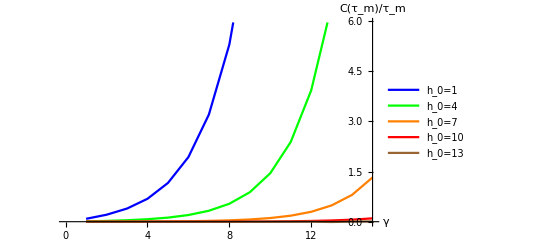

F:\ThesisProject\RESULTS\01062023_testanasim\ratio.png

```mathematica
ListLinePlot[lstRatio,AxesLabel->{"γ","C(τ_m)/τ_m"},PlotLegends->{"h_0=1","h_0=4","h_0=7","h_0=10","h_0=13"},PlotStyle->{Blue,Green,Orange,Red,Brown},AxesOrigin->{15,0}]
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ratio.png",%]
```

```mathematica
Rasterize[ListLinePlot[{lstRatio[[4,All]],lstRatio[[5,All]]},PlotStyle->{Red,Brown}]]
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ratio_inset.png",%]
```

-Graphics-

F:\ThesisProject\RESULTS\01062023_testanasim\ratio_inset.png

```mathematica
(*Examine eigenvalue*)

lst=Table[0,4,61];
For[gg=0,gg<4,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->7,h->(2*gg+5)};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},PlotRange->All,Joined->True]]
```

General::munfl: Exp[-3680.64] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3557.96] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3435.27] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Rasterize[ListPlot[lst[[2;;4,All]],PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},PlotRange->All,Joined->True]]
Export["F:\\ThesisProject\\RESULTS\\07062023_ana\\corr_hlines_2ip5.dat",lst]
```

-Graphics-

F:\ThesisProject\RESULTS\07062023_ana\corr_hlines_2ip5.dat

```mathematica
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];Print[N[seigenVa]];
Print[N[nseigenVeL]]]
```

```mathematica
(*08.06.2023 Expansion*)
Eigensystem[{{0,a,a,0},{1/a,0,0,a},{1/a,0,0,a},{0,1/a,1/a,0}}]
```

{{0,0,-2,2},{{-a^2,0,0,1},{0,-1,1,0},{a^2,-a,-a,1},{a^2,a,a,1}}}

```mathematica
Eigensystem[Transpose[{{0,a,a,0},{1/a,0,0,a},{1/a,0,0,a},{0,1/a,1/a,0}}]]
```

{{0,0,-2,2},{{-1/a^2,0,0,1},{0,-1,1,0},{1/a^2,-1/a,-1/a,1},{1/a^2,1/a,1/a,1}}}

```mathematica
eigenVa
```

{0,-2 ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,1],ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,2],ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,3]}

```mathematica
nessDist//MatrixForm
```

LinearSolveFunction[…]

```mathematica
MatrixRank[matJump]
```

6

```mathematica
nessDist
```

{ⅇ^g/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+h)/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+h)/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(2 h)/((1+ⅇ^g) (1+ⅇ^h)^2),1/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^h/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^h/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+2 h)/((1+ⅇ^g) (1+ⅇ^h)^2)}

```mathematica
lst=Table[0,8,201];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-10,0,0.1}]~Join~Table[fCtauP[i],{i,1,10,0.1}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-10,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
Export["F:\\ThesisProject\\RESULTS\\08062023_expasion\\corr_zeroorder.png",%]
```

F:\ThesisProject\RESULTS\08062023_expasion\corr_zeroorder.png

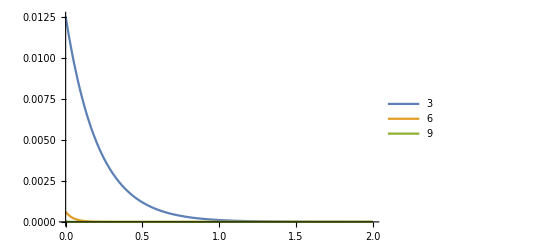

```mathematica
f0corr[g_,h_,t_]:=(E^(2 h-E^(-h/2) (1+E^h) t) (-1+E^g) (1+3 E^h+2 E^(2 h)))/((1+4 E^h) (1+E^(2 h)) (2+E^g+4 E^h+E^(2 h)+2 E^(g+h)+2 E^(g+2 h)));
Plot[{f0corr[7,3,t],f0corr[7,6,t],f0corr[7,9,t]},{t,0,2},PlotLegends->{3,6,9},PlotRange->All]
```

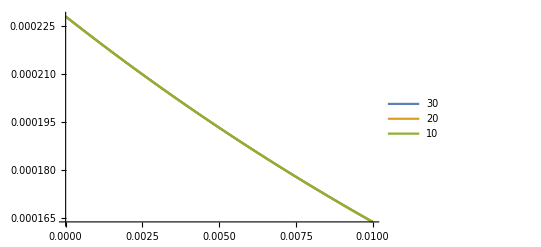

```mathematica
Plot[{fCtauP[t]/.{g->30,h->7},fCtauP[t]/.{g->20,h->7},fCtauP[t]/.{g->10,h->7}},{t,0,0.01},PlotRange->All,PlotLegends->{30,20,10}]
```

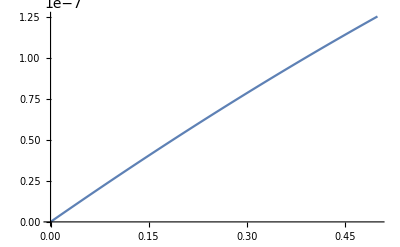

```mathematica
Plot[(Exp[x]-1)/(2*Exp[x+7]+2*Exp[x+14]+Exp[x]+4*Exp[7]+Exp[14]+2),{x,0,0.5}]
```

```mathematica
(*09.06.2023 Closer to corr*)
lst=Table[0,5,31];
For[gg=1,gg<=5,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg*2,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg]]=Table[fCtauP[i],{i,0,6,0.2}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,2,10,2}],DataRange->{0,6},PlotRange->All,Joined->True]]
```

General::munfl: Exp[-713.419] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-738.898] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-764.377] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
lstn=Table[0,15];
lstp=Table[0,15];
lstd=Table[0,15];
For[gg=1,gg<=15,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lstn[[gg]]=fCtauN[0];lstp[[gg]]=fCtauP[0];];
lstd=lstp-lstn
lstn
lstp
```

General::munfl: 9.16972×10^-152 (-4.11653×10^-160) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{6.93223×10^-13,8.96372×10^-12,2.02935×10^-11,1.33589×10^-11,-4.69624×10^-13,-2.18185×10^-11,1.44781×10^-8,-6.09801×10^-12,3.05054×10^-11,2.01195×10^-12,-1.53296×10^-10,-3.05682×10^-10,4.67217×10^-9,-2.94254×10^-8,1.32346×10^-8}

{0.00285236,0.00527807,0.0071108,0.00840853,0.00929614,0.00988645,0.0102691,0.010512,0.0106638,0.0107576,0.0108151,0.0108503,0.0108717,0.0108848,0.0108927}

{0.00285236,0.00527807,0.0071108,0.00840853,0.00929614,0.00988645,0.0102691,0.010512,0.0106638,0.0107576,0.0108151,0.0108503,0.0108717,0.0108847,0.0108927}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\09062023_testonfeed\\diff_t0.dat",{lstd,lstp,lstn}]
```

F:\ThesisProject\RESULTS\09062023_testonfeed\diff_t0.dat

```mathematica
Rasterize[Plot[{conditionP[t,1,1],conditionP[t,1,2],conditionP[t,1,3],conditionP[t,1,4],conditionP[t,1,5],conditionP[t,1,6],conditionP[t,1,7],conditionP[t,1,8]},{t,0,10},PlotLegends->Placed[{"From (0,0,0)","From (1,0,0)","From (0,1,0)","From (1,1,0)", "From (0,0,1)","From (1,0,1)","From (0,1,1)","From (1,1,1)"},{0.8,0.4}],LabelStyle->7,AxesLabel->{"time","P(0,0,0)"},PlotRange->{-0.1,1.1}]]
Export["F:\\ThesisProject\\RESULTS\\22062023_complementary\\transient_eq_tos1.png",%]
```

-Graphics-

F:\ThesisProject\RESULTS\22062023_complementary\transient_eq_tos1.png

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->15,h->6};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
Rasterize[Plot[{conditionP[t,8,1],conditionP[t,8,2],conditionP[t,8,3],conditionP[t,8,4],conditionP[t,8,5],conditionP[t,8,6],conditionP[t,8,7],conditionP[t,8,8]},{t,0,20},PlotLegends->Placed[{"From (0,0,0)","From (1,0,0)","From (0,1,0)","From (1,1,0)", "From (0,0,1)","From (1,0,1)","From (0,1,1)","From (1,1,1)"},{0.8,0.4}],LabelStyle->7,AxesLabel->{"time","P(1,1,1)"},PlotRange->{-0.1,1.1}]]
Export["F:\\ThesisProject\\RESULTS\\22062023_complementary\\transient_neq_tos8.png",%]
```

General::munfl: -7.25934×10^-151 (-2.69281×10^-158) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

F:\ThesisProject\RESULTS\22062023_complementary\transient_neq_tos8.png